## Assignment 5

6.1.2

(2) A grounded toroidal conducting shell has a shape given by the equation z^2/2 + (r-R)^2=a^2 where (r,θ,z) are cylindrical coordinates, and R=1 meter , a=0.75 meter. Plot this shell using a ParametricPlot3D command. The shell is filled with a uniform charge density ρ/ϵ_o=10 V. Find and plot the contours of constant electrostatic potential in the (r,z)plane. At what r and z is the potential maximum, and what is its value, to three significant figures?  (Hint: Solve Poisson's equation in cylindrical coordinates.)

### Solution

a) Plot the torus:

```mathematica
Clear["Global`*"]
```

```mathematica
R = 1; a = 0.75;
```

```mathematica
z[θ_]=Sqrt[2] a Sin[θ];
r[θ_] = a Cos[θ] + R;
ParametricPlot3D[{r[θ]Cos[ϕ],r[θ]Sin[ϕ],z[θ]},{θ,0,2Pi},{ϕ,0,2Pi}]
```

-Graphics3D-

b) Galerkin method for this system: work in cylindrical coordinates (r,z).

```mathematica
Clear[r,z]
```

```mathematica
(* define the curve that determines the boundary: *)
 Z[r_,z_] = z^2/2 + (r-R)^2 - a^2;
(* define the charge density  *)
ρ[r_,z_] = 10;
(* define the function u used to match inhomogeneous boundary conditions, if any *)
u[r_,z_] = 0;
```

```mathematica
(* define the inner product *)
norm[f_,g_] := NIntegrate[r f g Boole[Z[r,z]<0],{z,-Sqrt[2]a,Sqrt[2]a},{r,R-a,R+a}]
```

```mathematica
galerkin[Px_,Py_] := Module[{v,Lmat,ρvec,eq,eqns,vars},
(* define the basis functions (use symmetry in z) *)
v[i_,j_,r_,z_] = r^i z^(2j)    Z[r,z];
(* define the operator: *)
L[f_] :=1/r D[r D[f,r],r] + D[f,{z,2}];
(* determine the projection of the operator onto the basis functions *)
Lmat[i_,j_,k_,l_] := norm[v[i,j,r,z], L[v[k,l,r,z]]];
(* determine the projection of ρ̄ onto the basis functions: *)
ρvec[i_,j_] := norm[v[i,j,r,z], -ρ[r,z]];
(* define the equations for the Fourier coefficients c[m,n] *)
eq[i_,j_] :=eq[i,j] = Sum[Lmat[i,j,k,l]c[k,l],{k,0,Px},{l,0,Py}] == ρvec[i,j];
(* Print out the equations (not necessary, but a useful check) *)
Do[Print["eq",{i,j}," = ",eq[i,j]],{i,0,Px},{j,0,Py}];
(* create lists of equations and variables *)
eqns = Flatten[Table[eq[i,j],{i,0,Px},{j,0,Py}]];
vars = Flatten[Table[c[k,l],{k,0,Px},{l,0,Py}]];
(* solve the equations *)
coefficients = Solve[eqns,vars][[1]];
(* define the solution *)
ϕ[r_,z_] =  Sum[c[k,l] v[k,l,r,z],{k,0,Px},{l,0,Py}]/.coefficients;]
```

```mathematica
galerkin[1,1]
```

eq{0,0} = -2.10863 c[0,0]-0.395369 c[0,1]-2.43811 c[1,0]-0.441701 c[1,1]==7.02878

eq{0,1} = -0.395369 c[0,0]-0.31506 c[0,1]-0.441701 c[1,0]-0.339037 c[1,1]==1.3179

eq{1,0} = -2.43811 c[0,0]-0.441701 c[0,1]-3.22885 c[1,0]-0.552899 c[1,1]==7.68773

eq{1,1} = -0.441701 c[0,0]-0.339037 c[0,1]-0.552899 c[1,0]-0.393245 c[1,1]==1.41056

```mathematica
FindMaximum[ϕ[r,0],{r,.9}]
```

{2.00294,{r→0.91654}}

```mathematica
galerkin[2,2]
```

eq{0,0} = -2.10863 c[0,0]-0.395369 c[0,1]-0.166796 c[0,2]-2.43811 c[1,0]-0.441701 c[1,1]-0.182433 c[1,2]-2.96527 c[2,0]-0.515833 c[2,1]-0.207453 c[2,2]==7.02878

eq{0,1} = -0.395369 c[0,0]-0.31506 c[0,1]-0.193901 c[0,2]-0.441701 c[1,0]-0.339037 c[1,1]-0.205922 c[1,2]-0.515833 c[2,0]-0.380736 c[2,1]-0.227032 c[2,2]==1.3179

eq{0,2} = -0.166796 c[0,0]-0.193901 c[0,1]-0.155394 c[0,2]-0.182433 c[1,0]-0.205922 c[1,1]-0.163287 c[1,2]-0.207453 c[2,0]-0.227032 c[2,1]-0.177423 c[2,2]==0.555987

eq{1,0} = -2.43811 c[0,0]-0.441701 c[0,1]-0.182433 c[0,2]-3.22885 c[1,0]-0.552899 c[1,1]-0.219963 c[1,2]-4.32383 c[2,0]-0.703884 c[2,1]-0.270246 c[2,2]==7.68773

eq{1,1} = -0.441701 c[0,0]-0.339037 c[0,1]-0.205922 c[0,2]-0.552899 c[1,0]-0.393245 c[1,1]-0.232896 c[1,2]-0.703884 c[2,0]-0.469721 c[2,1]-0.270879 c[2,2]==1.41056

eq{1,2} = -0.182433 c[0,0]-0.205922 c[0,1]-0.163287 c[0,2]-0.219963 c[1,0]-0.232896 c[1,1]-0.180722 c[1,2]-0.270246 c[2,0]-0.270879 c[2,1]-0.205464 c[2,2]==0.587262

eq{2,0} = -2.96527 c[0,0]-0.515833 c[0,1]-0.207453 c[0,2]-4.32383 c[1,0]-0.703884 c[1,1]-0.270246 c[1,2]-6.20904 c[2,0]-0.956742 c[2,1]-0.352829 c[2,2]==9.00562

eq{2,1} = -0.515833 c[0,0]-0.380736 c[0,1]-0.227032 c[0,2]-0.703884 c[1,0]-0.469721 c[1,1]-0.270879 c[1,2]-0.956743 c[2,0]-0.590355 c[2,1]-0.329694 c[2,2]==1.59589

eq{2,2} = -0.207453 c[0,0]-0.227032 c[0,1]-0.177423 c[0,2]-0.270246 c[1,0]-0.270879 c[1,1]-0.205464 c[1,2]-0.352829 c[2,0]-0.329694 c[2,1]-0.243 c[2,2]==0.64981

```mathematica
FindMaximum[ϕ[r,z],{r,.9},{z,0}]
```

{1.98199,{r→0.884773,z→0.}}

```mathematica
galerkin[3,3]
```

eq{0,0} = -2.10863 c[0,0]-0.395369 c[0,1]-0.166796 c[0,2]-0.0938229 c[0,3]-2.43811 c[1,0]-0.441701 c[1,1]-0.182433 c[1,2]-0.101153 c[1,3]-2.96527 c[2,0]-0.515833 c[2,1]-0.207453 c[2,2]-0.112881 c[2,3]-3.75961 c[3,0]-0.625582 c[3,1]-0.244054 c[3,2]-0.12989 c[3,3]==7.02878

eq{0,1} = -0.395369 c[0,0]-0.31506 c[0,1]-0.193901 c[0,2]-0.131938 c[0,3]-0.441701 c[1,0]-0.339037 c[1,1]-0.205922 c[1,2]-0.138889 c[1,3]-0.515833 c[2,0]-0.380736 c[2,1]-0.227032 c[2,2]-0.15114 c[2,3]-0.625582 c[3,0]-0.443528 c[3,1]-0.25868 c[3,2]-0.169426 c[3,3]==1.3179

eq{0,2} = -0.166796 c[0,0]-0.193901 c[0,1]-0.155394 c[0,2]-0.123692 c[0,3]-0.182433 c[1,0]-0.205922 c[1,1]-0.163287 c[1,2]-0.129084 c[1,3]-0.207453 c[2,0]-0.227032 c[2,1]-0.177423 c[2,2]-0.138825 c[2,3]-0.244054 c[3,0]-0.25868 c[3,1]-0.198635 c[3,2]-0.15342 c[3,3]==0.555987

eq{0,3} = -0.0938229 c[0,0]-0.131938 c[0,1]-0.123692 c[0,2]-0.109584 c[0,3]-0.101153 c[1,0]-0.138889 c[1,1]-0.129084 c[1,2]-0.113726 c[1,3]-0.112881 c[2,0]-0.15114 c[2,1]-0.138825 c[2,2]-0.121292 c[2,3]-0.12989 c[3,0]-0.169426 c[3,1]-0.15342 c[3,2]-0.132633 c[3,3]==0.312743

eq{1,0} = -2.43811 c[0,0]-0.441701 c[0,1]-0.182433 c[0,2]-0.101153 c[0,3]-3.22885 c[1,0]-0.552899 c[1,1]-0.219963 c[1,2]-0.118745 c[1,3]-4.32383 c[2,0]-0.703884 c[2,1]-0.270246 c[2,2]-0.142089 c[2,3]-5.88986 c[3,0]-0.913422 c[3,1]-0.338561 c[3,2]-0.173307 c[3,3]==7.68773

eq{1,1} = -0.441701 c[0,0]-0.339037 c[0,1]-0.205922 c[0,2]-0.138889 c[0,3]-0.552899 c[1,0]-0.393245 c[1,1]-0.232896 c[1,2]-0.154439 c[1,3]-0.703884 c[2,0]-0.469721 c[2,1]-0.270879 c[2,2]-0.176255 c[2,3]-0.913422 c[3,0]-0.576086 c[3,1]-0.323123 c[3,2]-0.205977 c[3,3]==1.41056

eq{1,2} = -0.182433 c[0,0]-0.205922 c[0,1]-0.163287 c[0,2]-0.129084 c[0,3]-0.219963 c[1,0]-0.232896 c[1,1]-0.180722 c[1,2]-0.140913 c[1,3]-0.270246 c[2,0]-0.270879 c[2,1]-0.205464 c[2,2]-0.157725 c[2,3]-0.33856 c[3,0]-0.323123 c[3,1]-0.239353 c[3,2]-0.180631 c[3,3]==0.587262

eq{1,3} = -0.101153 c[0,0]-0.138889 c[0,1]-0.129084 c[0,2]-0.113726 c[0,3]-0.118745 c[1,0]-0.154439 c[1,1]-0.140913 c[1,2]-0.122727 c[1,3]-0.142089 c[2,0]-0.176255 c[2,1]-0.157725 c[2,2]-0.135583 c[2,3]-0.173307 c[3,0]-0.205977 c[3,1]-0.180631 c[3,2]-0.153054 c[3,3]==0.327403

eq{2,0} = -2.96527 c[0,0]-0.515833 c[0,1]-0.207453 c[0,2]-0.112881 c[0,3]-4.32383 c[1,0]-0.703884 c[1,1]-0.270246 c[1,2]-0.142089 c[1,3]-6.20904 c[2,0]-0.956742 c[2,1]-0.352829 c[2,2]-0.179877 c[2,3]-8.9233 c[3,0]-1.30771 c[3,1]-0.464426 c[3,2]-0.229907 c[3,3]==9.00562

eq{2,1} = -0.515833 c[0,0]-0.380736 c[0,1]-0.227032 c[0,2]-0.15114 c[0,3]-0.703884 c[1,0]-0.469721 c[1,1]-0.270879 c[1,2]-0.176255 c[1,3]-0.956743 c[2,0]-0.590355 c[2,1]-0.329694 c[2,2]-0.209623 c[2,3]-1.30771 c[3,0]-0.755614 c[3,1]-0.408933 c[3,2]-0.253972 c[3,3]==1.59589

eq{2,2} = -0.207453 c[0,0]-0.227032 c[0,1]-0.177423 c[0,2]-0.138825 c[0,3]-0.270246 c[1,0]-0.270879 c[1,1]-0.205464 c[1,2]-0.157725 c[1,3]-0.352829 c[2,0]-0.329694 c[2,1]-0.243 c[2,2]-0.182914 c[2,3]-0.464426 c[3,0]-0.408933 c[3,1]-0.293071 c[3,2]-0.216209 c[3,3]==0.64981

eq{2,3} = -0.112881 c[0,0]-0.15114 c[0,1]-0.138825 c[0,2]-0.121292 c[0,3]-0.142089 c[1,0]-0.176255 c[1,1]-0.157725 c[1,2]-0.135583 c[1,3]-0.179877 c[2,0]-0.209623 c[2,1]-0.182914 c[2,2]-0.15461 c[2,3]-0.229907 c[3,0]-0.253972 c[3,1]-0.216209 c[3,2]-0.179604 c[3,3]==0.356722

eq{3,0} = -3.75961 c[0,0]-0.625582 c[0,1]-0.244054 c[0,2]-0.12989 c[0,3]-5.88986 c[1,0]-0.913422 c[1,1]-0.338561 c[1,2]-0.173307 c[1,3]-8.9233 c[2,0]-1.30771 c[2,1]-0.464426 c[2,2]-0.229907 c[2,3]-13.3761 c[3,0]-1.86362 c[3,1]-0.636583 c[3,2]-0.305517 c[3,3]==11.1215

eq{3,1} = -0.625582 c[0,0]-0.443528 c[0,1]-0.25868 c[0,2]-0.169426 c[0,3]-0.913422 c[1,0]-0.576086 c[1,1]-0.323123 c[1,2]-0.205977 c[1,3]-1.30771 c[2,0]-0.755614 c[2,1]-0.408933 c[2,2]-0.253972 c[2,3]-1.86362 c[3,0]-1.00268 c[3,1]-0.524595 c[3,2]-0.317591 c[3,3]==1.88952

eq{3,2} = -0.244054 c[0,0]-0.25868 c[0,1]-0.198635 c[0,2]-0.15342 c[0,3]-0.338561 c[1,0]-0.323123 c[1,1]-0.239353 c[1,2]-0.180631 c[1,3]-0.464426 c[2,0]-0.408933 c[2,1]-0.293071 c[2,2]-0.216209 c[2,3]-0.636583 c[3,0]-0.524595 c[3,1]-0.364425 c[3,2]-0.262887 c[3,3]==0.748031

eq{3,3} = -0.12989 c[0,0]-0.169426 c[0,1]-0.15342 c[0,2]-0.132633 c[0,3]-0.173307 c[1,0]-0.205977 c[1,1]-0.180631 c[1,2]-0.153054 c[1,3]-0.229907 c[2,0]-0.253972 c[2,1]-0.216209 c[2,2]-0.179604 c[2,3]-0.305517 c[3,0]-0.317591 c[3,1]-0.262887 c[3,2]-0.214119 c[3,3]==0.402469

```mathematica
FindMaximum[ϕ[r,z],{r,.9},{z,0}]
```

{1.96501,{r→0.892534,z→0.}}

```mathematica
galerkin[4,4]
```

eq{0,0} = -2.10863 c[0,0]-0.395369 c[0,1]-0.166796 c[0,2]-0.0938229 c[0,3]-0.0615713 c[0,4]-2.43811 c[1,0]-0.441701 c[1,1]-0.182433 c[1,2]-0.101153 c[1,3]-0.0656943 c[1,4]-2.96527 c[2,0]-0.515833 c[2,1]-0.207453 c[2,2]-0.112881 c[2,3]-0.0722913 c[2,4]-3.75961 c[3,0]-0.625582 c[3,1]-0.244054 c[3,2]-0.12989 c[3,3]-0.0817969 c[3,4]-4.93233 c[4,0]-0.78346 c[4,1]-0.295754 c[4,2]-0.153594 c[4,3]-0.094907 c[4,4]==7.02878

eq{0,1} = -0.395369 c[0,0]-0.31506 c[0,1]-0.193901 c[0,2]-0.131938 c[0,3]-0.0973046 c[0,4]-0.441701 c[1,0]-0.339037 c[1,1]-0.205922 c[1,2]-0.138889 c[1,3]-0.101769 c[1,4]-0.515833 c[2,0]-0.380736 c[2,1]-0.227032 c[2,2]-0.15114 c[2,3]-0.109654 c[2,4]-0.625582 c[3,0]-0.443528 c[3,1]-0.25868 c[3,2]-0.169426 c[3,3]-0.121379 c[3,4]-0.78346 c[4,0]-0.533279 c[4,1]-0.303411 c[4,2]-0.195038 c[4,3]-0.137683 c[4,4]==1.3179

eq{0,2} = -0.166796 c[0,0]-0.193901 c[0,1]-0.155394 c[0,2]-0.123692 c[0,3]-0.101234 c[0,4]-0.182433 c[1,0]-0.205922 c[1,1]-0.163287 c[1,2]-0.129084 c[1,3]-0.105115 c[1,4]-0.207453 c[2,0]-0.227032 c[2,1]-0.177423 c[2,2]-0.138825 c[2,3]-0.11216 c[2,4]-0.244054 c[3,0]-0.25868 c[3,1]-0.198635 c[3,2]-0.15342 c[3,3]-0.122696 c[3,4]-0.295754 c[4,0]-0.303411 c[4,1]-0.228414 c[4,2]-0.173782 c[4,3]-0.137317 c[4,4]==0.555987

eq{0,3} = -0.0938229 c[0,0]-0.131938 c[0,1]-0.123692 c[0,2]-0.109584 c[0,3]-0.0968641 c[0,4]-0.101153 c[1,0]-0.138889 c[1,1]-0.129084 c[1,2]-0.113726 c[1,3]-0.100113 c[1,4]-0.112881 c[2,0]-0.15114 c[2,1]-0.138825 c[2,2]-0.121292 c[2,3]-0.106086 c[2,4]-0.12989 c[3,0]-0.169426 c[3,1]-0.15342 c[3,2]-0.132633 c[3,3]-0.115033 c[3,4]-0.153594 c[4,0]-0.195038 c[4,1]-0.173782 c[4,2]-0.148385 c[4,3]-0.127412 c[4,4]==0.312743

eq{0,4} = -0.0615713 c[0,0]-0.0973046 c[0,1]-0.101234 c[0,2]-0.0968641 c[0,3]-0.0907697 c[0,4]-0.0656943 c[1,0]-0.101769 c[1,1]-0.105115 c[1,2]-0.100113 c[1,3]-0.093493 c[1,4]-0.0722913 c[2,0]-0.109654 c[2,1]-0.11216 c[2,2]-0.106086 c[2,3]-0.0985371 c[2,4]-0.0817969 c[3,0]-0.121379 c[3,1]-0.122696 c[3,2]-0.115033 c[3,3]-0.106093 c[3,4]-0.094907 c[4,0]-0.137683 c[4,1]-0.137317 c[4,2]-0.127412 c[4,3]-0.116517 c[4,4]==0.205238

eq{1,0} = -2.43811 c[0,0]-0.441701 c[0,1]-0.182433 c[0,2]-0.101153 c[0,3]-0.0656943 c[0,4]-3.22885 c[1,0]-0.552899 c[1,1]-0.219963 c[1,2]-0.118745 c[1,3]-0.0755897 c[1,4]-4.32383 c[2,0]-0.703884 c[2,1]-0.270246 c[2,2]-0.142089 c[2,3]-0.0886257 c[2,4]-5.88986 c[3,0]-0.913422 c[3,1]-0.338561 c[3,2]-0.173307 c[3,3]-0.105846 c[3,4]-8.16749 c[4,0]-1.20797 c[4,1]-0.432228 c[4,2]-0.215303 c[4,3]-0.128667 c[4,4]==7.68773

eq{1,1} = -0.441701 c[0,0]-0.339037 c[0,1]-0.205922 c[0,2]-0.138889 c[0,3]-0.101769 c[0,4]-0.552899 c[1,0]-0.393245 c[1,1]-0.232896 c[1,2]-0.154439 c[1,3]-0.111742 c[1,4]-0.703884 c[2,0]-0.469721 c[2,1]-0.270879 c[2,2]-0.176255 c[2,3]-0.125684 c[2,4]-0.913422 c[3,0]-0.576086 c[3,1]-0.323123 c[3,2]-0.205977 c[3,3]-0.144532 c[3,4]-1.20797 c[4,0]-0.723416 c[4,1]-0.394329 c[4,2]-0.245962 c[4,3]-0.16962 c[4,4]==1.41056

eq{1,2} = -0.182433 c[0,0]-0.205922 c[0,1]-0.163287 c[0,2]-0.129084 c[0,3]-0.105115 c[0,4]-0.219963 c[1,0]-0.232896 c[1,1]-0.180722 c[1,2]-0.140913 c[1,3]-0.113595 c[1,4]-0.270246 c[2,0]-0.270879 c[2,1]-0.205464 c[2,2]-0.157725 c[2,3]-0.125647 c[2,4]-0.33856 c[3,0]-0.323123 c[3,1]-0.239353 c[3,2]-0.180631 c[3,3]-0.141985 c[3,4]-0.432228 c[4,0]-0.394329 c[4,1]-0.28506 c[4,2]-0.21124 c[4,3]-0.163648 c[4,4]==0.587262

eq{1,3} = -0.101153 c[0,0]-0.138889 c[0,1]-0.129084 c[0,2]-0.113726 c[0,3]-0.100113 c[0,4]-0.118745 c[1,0]-0.154439 c[1,1]-0.140913 c[1,2]-0.122727 c[1,3]-0.107136 c[1,4]-0.142089 c[2,0]-0.176255 c[2,1]-0.157725 c[2,2]-0.135583 c[2,3]-0.117186 c[2,4]-0.173307 c[3,0]-0.205977 c[3,1]-0.180631 c[3,2]-0.153054 c[3,3]-0.130801 c[3,4]-0.215303 c[4,0]-0.245962 c[4,1]-0.21124 c[4,2]-0.176244 c[4,3]-0.148767 c[4,4]==0.327403

eq{1,4} = -0.0656943 c[0,0]-0.101769 c[0,1]-0.105115 c[0,2]-0.100113 c[0,3]-0.093493 c[0,4]-0.0755897 c[1,0]-0.111742 c[1,1]-0.113595 c[1,2]-0.107136 c[1,3]-0.099342 c[1,4]-0.0886257 c[2,0]-0.125684 c[2,1]-0.125647 c[2,2]-0.117186 c[2,3]-0.107741 c[2,4]-0.105846 c[3,0]-0.144532 c[3,1]-0.141985 c[3,2]-0.130801 c[3,3]-0.119101 c[3,4]-0.128667 c[4,0]-0.16962 c[4,1]-0.163648 c[4,2]-0.148767 c[4,3]-0.134023 c[4,4]==0.213484

eq{2,0} = -2.96527 c[0,0]-0.515833 c[0,1]-0.207453 c[0,2]-0.112881 c[0,3]-0.0722913 c[0,4]-4.32383 c[1,0]-0.703884 c[1,1]-0.270246 c[1,2]-0.142089 c[1,3]-0.0886257 c[1,4]-6.20904 c[2,0]-0.956742 c[2,1]-0.352829 c[2,2]-0.179877 c[2,3]-0.109492 c[2,4]-8.9233 c[3,0]-1.30771 c[3,1]-0.464426 c[3,2]-0.229907 c[3,3]-0.136677 c[3,4]-12.9116 c[4,0]-1.80424 c[4,1]-0.617856 c[4,2]-0.297172 c[4,3]-0.172576 c[4,4]==9.00562

eq{2,1} = -0.515833 c[0,0]-0.380736 c[0,1]-0.227032 c[0,2]-0.15114 c[0,3]-0.109654 c[0,4]-0.703884 c[1,0]-0.469721 c[1,1]-0.270879 c[1,2]-0.176255 c[1,3]-0.125684 c[1,4]-0.956743 c[2,0]-0.590355 c[2,1]-0.329694 c[2,2]-0.209623 c[2,3]-0.146815 c[2,4]-1.30771 c[3,0]-0.755614 c[3,1]-0.408933 c[3,2]-0.253972 c[3,3]-0.174589 c[3,4]-1.80424 c[4,0]-0.983952 c[4,1]-0.516251 c[4,2]-0.313078 c[4,3]-0.211121 c[4,4]==1.59589

eq{2,2} = -0.207453 c[0,0]-0.227032 c[0,1]-0.177423 c[0,2]-0.138825 c[0,3]-0.11216 c[0,4]-0.270246 c[1,0]-0.270879 c[1,1]-0.205464 c[1,2]-0.157725 c[1,3]-0.125647 c[1,4]-0.352829 c[2,0]-0.329694 c[2,1]-0.243 c[2,2]-0.182914 c[2,3]-0.143541 c[2,4]-0.464426 c[3,0]-0.408933 c[3,1]-0.293071 c[3,2]-0.216209 c[3,3]-0.167008 c[3,4]-0.617856 c[4,0]-0.516251 c[4,1]-0.359912 c[4,2]-0.26012 c[4,3]-0.197646 c[4,4]==0.64981

eq{2,3} = -0.112881 c[0,0]-0.15114 c[0,1]-0.138825 c[0,2]-0.121292 c[0,3]-0.106086 c[0,4]-0.142089 c[1,0]-0.176255 c[1,1]-0.157725 c[1,2]-0.135583 c[1,3]-0.117186 c[1,4]-0.179877 c[2,0]-0.209623 c[2,1]-0.182914 c[2,2]-0.15461 c[2,3]-0.131931 c[2,4]-0.229907 c[3,0]-0.253972 c[3,1]-0.216209 c[3,2]-0.179604 c[3,3]-0.151192 c[3,4]-0.297172 c[4,0]-0.313078 c[4,1]-0.26012 c[4,2]-0.212265 c[4,3]-0.176158 c[4,4]==0.356722

eq{2,4} = -0.0722913 c[0,0]-0.109654 c[0,1]-0.11216 c[0,2]-0.106086 c[0,3]-0.0985371 c[0,4]-0.0886257 c[1,0]-0.125684 c[1,1]-0.125647 c[1,2]-0.117186 c[1,3]-0.107741 c[1,4]-0.109492 c[2,0]-0.146815 c[2,1]-0.143541 c[2,2]-0.131931 c[2,3]-0.119963 c[2,4]-0.136677 c[3,0]-0.174589 c[3,1]-0.167008 c[3,2]-0.151192 c[3,3]-0.135862 c[3,4]-0.172576 c[4,0]-0.211121 c[4,1]-0.197646 c[4,2]-0.176158 c[4,3]-0.156338 c[4,4]==0.229976

eq{3,0} = -3.75961 c[0,0]-0.625582 c[0,1]-0.244054 c[0,2]-0.12989 c[0,3]-0.0817969 c[0,4]-5.88986 c[1,0]-0.913422 c[1,1]-0.338561 c[1,2]-0.173307 c[1,3]-0.105846 c[1,4]-8.9233 c[2,0]-1.30771 c[2,1]-0.464426 c[2,2]-0.229907 c[2,3]-0.136677 c[2,4]-13.3761 c[3,0]-1.86362 c[3,1]-0.636583 c[3,2]-0.305517 c[3,3]-0.177089 c[3,4]-20.0278 c[4,0]-2.66158 c[4,1]-0.876207 c[4,2]-0.408209 c[4,3]-0.230891 c[4,4]==11.1215

eq{3,1} = -0.625582 c[0,0]-0.443528 c[0,1]-0.25868 c[0,2]-0.169426 c[0,3]-0.121379 c[0,4]-0.913422 c[1,0]-0.576086 c[1,1]-0.323123 c[1,2]-0.205977 c[1,3]-0.144532 c[1,4]-1.30771 c[2,0]-0.755614 c[2,1]-0.408933 c[2,2]-0.253972 c[2,3]-0.174589 c[2,4]-1.86362 c[3,0]-1.00268 c[3,1]-0.524595 c[3,2]-0.317591 c[3,3]-0.213888 c[3,4]-2.66158 c[4,0]-1.34673 c[4,1]-0.682025 c[4,2]-0.402608 c[4,3]-0.265618 c[4,4]==1.88952

eq{3,2} = -0.244054 c[0,0]-0.25868 c[0,1]-0.198635 c[0,2]-0.15342 c[0,3]-0.122696 c[0,4]-0.338561 c[1,0]-0.323123 c[1,1]-0.239353 c[1,2]-0.180631 c[1,3]-0.141985 c[1,4]-0.464426 c[2,0]-0.408933 c[2,1]-0.293071 c[2,2]-0.216209 c[2,3]-0.167008 c[2,4]-0.636583 c[3,0]-0.524595 c[3,1]-0.364425 c[3,2]-0.262887 c[3,3]-0.1995 c[3,4]-0.876207 c[4,0]-0.682025 c[4,1]-0.459847 c[4,2]-0.324414 c[4,3]-0.241812 c[4,4]==0.748031

eq{3,3} = -0.12989 c[0,0]-0.169426 c[0,1]-0.15342 c[0,2]-0.132633 c[0,3]-0.115033 c[0,4]-0.173307 c[1,0]-0.205977 c[1,1]-0.180631 c[1,2]-0.153054 c[1,3]-0.130801 c[1,4]-0.229907 c[2,0]-0.253972 c[2,1]-0.216209 c[2,2]-0.179604 c[2,3]-0.151192 c[2,4]-0.305517 c[3,0]-0.317591 c[3,1]-0.262887 c[3,2]-0.214119 c[3,3]-0.177485 c[3,4]-0.408209 c[4,0]-0.402608 c[4,1]-0.324414 c[4,2]-0.259087 c[4,3]-0.211407 c[4,4]==0.402469

eq{3,4} = -0.0817969 c[0,0]-0.121379 c[0,1]-0.122696 c[0,2]-0.115033 c[0,3]-0.106093 c[0,4]-0.105846 c[1,0]-0.144532 c[1,1]-0.141985 c[1,2]-0.130801 c[1,3]-0.119101 c[1,4]-0.136677 c[2,0]-0.174589 c[2,1]-0.167008 c[2,2]-0.151192 c[2,3]-0.135862 c[2,4]-0.177089 c[3,0]-0.213888 c[3,1]-0.1995 c[3,2]-0.177485 c[3,3]-0.157338 c[3,4]-0.230891 c[4,0]-0.265618 c[4,1]-0.241812 c[4,2]-0.211407 c[4,3]-0.184821 c[4,4]==0.255584

eq{4,0} = -4.93233 c[0,0]-0.78346 c[0,1]-0.295754 c[0,2]-0.153594 c[0,3]-0.094907 c[0,4]-8.16749 c[1,0]-1.20797 c[1,1]-0.432228 c[1,2]-0.215303 c[1,3]-0.128667 c[1,4]-12.9116 c[2,0]-1.80424 c[2,1]-0.617856 c[2,2]-0.297172 c[2,3]-0.172576 c[2,4]-20.0278 c[3,0]-2.66158 c[3,1]-0.876207 c[3,2]-0.408209 c[3,3]-0.230891 c[3,4]-30.8464 c[4,0]-3.91285 c[4,1]-1.24135 c[4,2]-0.561124 c[4,3]-0.309499 c[4,4]==14.3132

eq{4,1} = -0.78346 c[0,0]-0.533279 c[0,1]-0.303411 c[0,2]-0.195038 c[0,3]-0.137683 c[0,4]-1.20797 c[1,0]-0.723416 c[1,1]-0.394329 c[1,2]-0.245962 c[1,3]-0.16962 c[1,4]-1.80424 c[2,0]-0.983952 c[2,1]-0.516251 c[2,2]-0.313078 c[2,3]-0.211121 c[2,4]-2.66158 c[3,0]-1.34673 c[3,1]-0.682025 c[3,2]-0.402608 c[3,3]-0.265618 c[3,4]-3.91285 c[4,0]-1.85793 c[4,1]-0.909874 c[4,2]-0.523215 c[4,3]-0.337819 c[4,4]==2.32273

eq{4,2} = -0.295754 c[0,0]-0.303411 c[0,1]-0.228414 c[0,2]-0.173782 c[0,3]-0.137317 c[0,4]-0.432228 c[1,0]-0.394329 c[1,1]-0.28506 c[1,2]-0.21124 c[1,3]-0.163648 c[1,4]-0.617856 c[2,0]-0.516251 c[2,1]-0.359912 c[2,2]-0.26012 c[2,3]-0.197646 c[2,4]-0.876207 c[3,0]-0.682025 c[3,1]-0.459847 c[3,2]-0.324414 c[3,3]-0.241812 c[3,4]-1.24135 c[4,0]-0.909874 c[4,1]-0.594453 c[4,2]-0.409609 c[4,3]-0.299542 c[4,4]==0.89072

eq{4,3} = -0.153594 c[0,0]-0.195038 c[0,1]-0.173782 c[0,2]-0.148385 c[0,3]-0.127412 c[0,4]-0.215303 c[1,0]-0.245962 c[1,1]-0.21124 c[1,2]-0.176244 c[1,3]-0.148767 c[1,4]-0.297172 c[2,0]-0.313078 c[2,1]-0.26012 c[2,2]-0.212265 c[2,3]-0.176158 c[2,4]-0.408209 c[3,0]-0.402608 c[3,1]-0.324414 c[3,2]-0.259087 c[3,3]-0.211407 c[3,4]-0.561124 c[4,0]-0.523215 c[4,1]-0.409609 c[4,2]-0.320299 c[4,3]-0.256964 c[4,4]==0.468176

eq{4,4} = -0.094907 c[0,0]-0.137683 c[0,1]-0.137317 c[0,2]-0.127412 c[0,3]-0.116517 c[0,4]-0.128667 c[1,0]-0.16962 c[1,1]-0.163648 c[1,2]-0.148767 c[1,3]-0.134023 c[1,4]-0.172576 c[2,0]-0.211121 c[2,1]-0.197646 c[2,2]-0.176158 c[2,3]-0.156338 c[2,4]-0.230891 c[3,0]-0.265618 c[3,1]-0.241812 c[3,2]-0.211407 c[3,3]-0.184821 c[3,4]-0.309499 c[4,0]-0.337819 c[4,1]-0.299542 c[4,2]-0.256964 c[4,3]-0.221281 c[4,4]==0.292048

```mathematica
FindMaximum[ϕ[r,z],{r,.9},{z,0}]
```

{1.96689,{r→0.878749,z→0.}}

```mathematica
galerkin[5,5]
```

eq{0,0} = -2.10863 c[0,0]-0.395369 c[0,1]-0.166796 c[0,2]-0.0938229 c[0,3]-0.0615713 c[0,4]-0.0445292 c[0,5]-2.43811 c[1,0]-0.441701 c[1,1]-0.182433 c[1,2]-0.101153 c[1,3]-0.0656943 c[1,4]-0.0471384 c[1,5]-2.96527 c[2,0]-0.515833 c[2,1]-0.207453 c[2,2]-0.112881 c[2,3]-0.0722913 c[2,4]-0.051313 c[2,5]-3.75961 c[3,0]-0.625582 c[3,1]-0.244054 c[3,2]-0.12989 c[3,3]-0.0817969 c[3,4]-0.0572977 c[3,5]-4.93233 c[4,0]-0.78346 c[4,1]-0.295754 c[4,2]-0.153594 c[4,3]-0.094907 c[4,4]-0.0654838 c[4,5]-6.65587 c[5,0]-1.0085 c[5,1]-0.367833 c[5,2]-0.186093 c[5,3]-0.112646 c[5,4]-0.076444 c[5,5]==7.02878

eq{0,1} = -0.395369 c[0,0]-0.31506 c[0,1]-0.193901 c[0,2]-0.131938 c[0,3]-0.0973046 c[0,4]-0.0761867 c[0,5]-0.441701 c[1,0]-0.339037 c[1,1]-0.205922 c[1,2]-0.138889 c[1,3]-0.101769 c[1,4]-0.0792851 c[1,5]-0.515833 c[2,0]-0.380736 c[2,1]-0.227032 c[2,2]-0.15114 c[2,3]-0.109654 c[2,4]-0.0847643 c[2,5]-0.625582 c[3,0]-0.443528 c[3,1]-0.25868 c[3,2]-0.169426 c[3,3]-0.121379 c[3,4]-0.0928857 c[3,5]-0.78346 c[4,0]-0.533279 c[4,1]-0.303411 c[4,2]-0.195038 c[4,3]-0.137683 c[4,4]-0.104112 c[4,5]-1.0085 c[5,0]-0.659021 c[5,1]-0.365119 c[5,2]-0.229942 c[5,3]-0.159684 c[5,4]-0.119139 c[5,5]==1.3179

eq{0,2} = -0.166796 c[0,0]-0.193901 c[0,1]-0.155394 c[0,2]-0.123692 c[0,3]-0.101234 c[0,4]-0.0853839 c[0,5]-0.182433 c[1,0]-0.205922 c[1,1]-0.163287 c[1,2]-0.129084 c[1,3]-0.105115 c[1,4]-0.08831 c[1,5]-0.207453 c[2,0]-0.227032 c[2,1]-0.177423 c[2,2]-0.138825 c[2,3]-0.11216 c[2,4]-0.0936375 c[2,5]-0.244054 c[3,0]-0.25868 c[3,1]-0.198635 c[3,2]-0.15342 c[3,3]-0.122696 c[3,4]-0.101591 c[3,5]-0.295754 c[4,0]-0.303411 c[4,1]-0.228414 c[4,2]-0.173782 c[4,3]-0.137317 c[4,4]-0.112579 c[4,5]-0.367833 c[5,0]-0.365119 c[5,1]-0.26904 c[5,2]-0.201304 c[5,3]-0.156927 c[5,4]-0.12722 c[5,5]==0.555987

eq{0,3} = -0.0938229 c[0,0]-0.131938 c[0,1]-0.123692 c[0,2]-0.109584 c[0,3]-0.0968641 c[0,4]-0.0865723 c[0,5]-0.101153 c[1,0]-0.138889 c[1,1]-0.129084 c[1,2]-0.113726 c[1,3]-0.100113 c[1,4]-0.0891882 c[1,5]-0.112881 c[2,0]-0.15114 c[2,1]-0.138825 c[2,2]-0.121292 c[2,3]-0.106086 c[2,4]-0.0940177 c[2,5]-0.12989 c[3,0]-0.169426 c[3,1]-0.15342 c[3,2]-0.132633 c[3,3]-0.115033 c[3,4]-0.101245 c[3,5]-0.153594 c[4,0]-0.195038 c[4,1]-0.173782 c[4,2]-0.148385 c[4,3]-0.127412 c[4,4]-0.111208 c[4,5]-0.186093 c[5,0]-0.229942 c[5,1]-0.201304 c[5,2]-0.169523 c[5,3]-0.143918 c[5,4]-0.124424 c[5,5]==0.312743

eq{0,4} = -0.0615713 c[0,0]-0.0973046 c[0,1]-0.101234 c[0,2]-0.0968641 c[0,3]-0.0907697 c[0,4]-0.0849178 c[0,5]-0.0656943 c[1,0]-0.101769 c[1,1]-0.105115 c[1,2]-0.100113 c[1,3]-0.093493 c[1,4]-0.0872287 c[1,5]-0.0722913 c[2,0]-0.109654 c[2,1]-0.11216 c[2,2]-0.106086 c[2,3]-0.0985371 c[2,4]-0.09153 c[2,5]-0.0817969 c[3,0]-0.121379 c[3,1]-0.122696 c[3,2]-0.115033 c[3,3]-0.106093 c[3,4]-0.0979714 c[3,5]-0.094907 c[4,0]-0.137683 c[4,1]-0.137317 c[4,2]-0.127412 c[4,3]-0.116517 c[4,4]-0.106832 c[4,5]-0.112646 c[5,0]-0.159684 c[5,1]-0.156927 c[5,2]-0.143918 c[5,3]-0.130346 c[5,4]-0.118536 c[5,5]==0.205238

eq{0,5} = -0.0445292 c[0,0]-0.0761867 c[0,1]-0.0853839 c[0,2]-0.0865723 c[0,3]-0.0849178 c[0,4]-0.0824213 c[0,5]-0.0471384 c[1,0]-0.0792851 c[1,1]-0.08831 c[1,2]-0.0891882 c[1,3]-0.0872287 c[1,4]-0.0844681 c[1,5]-0.051313 c[2,0]-0.0847642 c[2,1]-0.0936375 c[2,2]-0.0940177 c[2,3]-0.0915299 c[2,4]-0.0882981 c[2,5]-0.0572977 c[3,0]-0.0928857 c[3,1]-0.101591 c[3,2]-0.101245 c[3,3]-0.0979714 c[3,4]-0.0940345 c[3,5]-0.0654838 c[4,0]-0.104112 c[4,1]-0.112579 c[4,2]-0.111208 c[4,3]-0.106832 c[4,4]-0.101908 c[4,5]-0.076444 c[5,0]-0.119139 c[5,1]-0.12722 c[5,2]-0.124424 c[5,3]-0.118536 c[5,4]-0.112269 c[5,5]==0.148431

eq{1,0} = -2.43811 c[0,0]-0.441701 c[0,1]-0.182433 c[0,2]-0.101153 c[0,3]-0.0656943 c[0,4]-0.0471384 c[0,5]-3.22885 c[1,0]-0.552899 c[1,1]-0.219963 c[1,2]-0.118745 c[1,3]-0.0755897 c[1,4]-0.0534003 c[1,5]-4.32383 c[2,0]-0.703884 c[2,1]-0.270246 c[2,2]-0.142089 c[2,3]-0.0886257 c[2,4]-0.0616027 c[2,5]-5.88986 c[3,0]-0.913422 c[3,1]-0.338561 c[3,2]-0.173307 c[3,3]-0.105846 c[3,4]-0.0723328 c[3,5]-8.16749 c[4,0]-1.20797 c[4,1]-0.432228 c[4,2]-0.215303 c[4,3]-0.128667 c[4,4]-0.0863807 c[4,5]-11.5179 c[5,0]-1.62609 c[5,1]-0.561675 c[5,2]-0.27214 c[5,3]-0.159039 c[5,4]-0.104822 c[5,5]==7.68773

eq{1,1} = -0.441701 c[0,0]-0.339037 c[0,1]-0.205922 c[0,2]-0.138889 c[0,3]-0.101769 c[0,4]-0.0792851 c[0,5]-0.552899 c[1,0]-0.393245 c[1,1]-0.232896 c[1,2]-0.154439 c[1,3]-0.111742 c[1,4]-0.0861993 c[1,5]-0.703884 c[2,0]-0.469721 c[2,1]-0.270879 c[2,2]-0.176255 c[2,3]-0.125684 c[2,4]-0.0958364 c[2,5]-0.913422 c[3,0]-0.576086 c[3,1]-0.323123 c[3,2]-0.205977 c[3,3]-0.144532 c[3,4]-0.10878 c[3,5]-1.20797 c[4,0]-0.723416 c[4,1]-0.394329 c[4,2]-0.245962 c[4,3]-0.16962 c[4,4]-0.12586 c[4,5]-1.62609 c[5,0]-0.927771 c[5,1]-0.491218 c[5,2]-0.299541 c[5,3]-0.20282 c[5,4]-0.148228 c[5,5]==1.41056

eq{1,2} = -0.182433 c[0,0]-0.205922 c[0,1]-0.163287 c[0,2]-0.129084 c[0,3]-0.105115 c[0,4]-0.08831 c[0,5]-0.219963 c[1,0]-0.232896 c[1,1]-0.180722 c[1,2]-0.140913 c[1,3]-0.113595 c[1,4]-0.0946869 c[1,5]-0.270246 c[2,0]-0.270879 c[2,1]-0.205464 c[2,2]-0.157725 c[2,3]-0.125647 c[2,4]-0.103743 c[2,5]-0.33856 c[3,0]-0.323123 c[3,1]-0.239353 c[3,2]-0.180631 c[3,3]-0.141985 c[3,4]-0.115968 c[3,5]-0.432228 c[4,0]-0.394329 c[4,1]-0.28506 c[4,2]-0.21124 c[4,3]-0.163648 c[4,4]-0.132069 c[4,5]-0.561675 c[5,0]-0.491218 c[5,1]-0.346375 c[5,2]-0.251819 c[5,3]-0.192084 c[5,4]-0.153029 c[5,5]==0.587262

eq{1,3} = -0.101153 c[0,0]-0.138889 c[0,1]-0.129084 c[0,2]-0.113726 c[0,3]-0.100113 c[0,4]-0.0891882 c[0,5]-0.118745 c[1,0]-0.154439 c[1,1]-0.140913 c[1,2]-0.122727 c[1,3]-0.107136 c[1,4]-0.0948226 c[1,5]-0.142089 c[2,0]-0.176255 c[2,1]-0.157725 c[2,2]-0.135583 c[2,3]-0.117186 c[2,4]-0.102892 c[2,5]-0.173307 c[3,0]-0.205977 c[3,1]-0.180631 c[3,2]-0.153054 c[3,3]-0.130801 c[3,4]-0.113793 c[3,5]-0.215303 c[4,0]-0.245962 c[4,1]-0.21124 c[4,2]-0.176244 c[4,3]-0.148767 c[4,4]-0.128102 c[4,5]-0.27214 c[5,0]-0.299541 c[5,1]-0.251819 c[5,2]-0.206702 c[5,3]-0.172176 c[5,4]-0.146618 c[5,5]==0.327403

eq{1,4} = -0.0656943 c[0,0]-0.101769 c[0,1]-0.105115 c[0,2]-0.100113 c[0,3]-0.093493 c[0,4]-0.0872287 c[0,5]-0.0755897 c[1,0]-0.111742 c[1,1]-0.113595 c[1,2]-0.107136 c[1,3]-0.099342 c[1,4]-0.0921714 c[1,5]-0.0886257 c[2,0]-0.125684 c[2,1]-0.125647 c[2,2]-0.117186 c[2,3]-0.107741 c[2,4]-0.099282 c[2,5]-0.105846 c[3,0]-0.144532 c[3,1]-0.141985 c[3,2]-0.130801 c[3,3]-0.119101 c[3,4]-0.108881 c[3,5]-0.128667 c[4,0]-0.16962 c[4,1]-0.163648 c[4,2]-0.148767 c[4,3]-0.134023 c[4,4]-0.121438 c[4,5]-0.159039 c[5,0]-0.20282 c[5,1]-0.192084 c[5,2]-0.172176 c[5,3]-0.153339 c[5,4]-0.1376 c[5,5]==0.213484

eq{1,5} = -0.0471384 c[0,0]-0.0792851 c[0,1]-0.08831 c[0,2]-0.0891882 c[0,3]-0.0872287 c[0,4]-0.0844681 c[0,5]-0.0534003 c[1,0]-0.0861993 c[1,1]-0.0946869 c[1,2]-0.0948226 c[1,3]-0.0921714 c[1,4]-0.0888254 c[1,5]-0.0616027 c[2,0]-0.0958364 c[2,1]-0.103743 c[2,2]-0.102892 c[2,3]-0.099282 c[2,4]-0.0951103 c[2,5]-0.0723328 c[3,0]-0.10878 c[3,1]-0.115968 c[3,2]-0.113793 c[3,3]-0.108881 c[3,4]-0.103586 c[3,5]-0.0863807 c[4,0]-0.12586 c[4,1]-0.132069 c[4,2]-0.128102 c[4,3]-0.121438 c[4,4]-0.114635 c[4,5]-0.104822 c[5,0]-0.148228 c[5,1]-0.153029 c[5,2]-0.146618 c[5,3]-0.1376 c[5,4]-0.128789 c[5,5]==0.153649

eq{2,0} = -2.96527 c[0,0]-0.515833 c[0,1]-0.207453 c[0,2]-0.112881 c[0,3]-0.0722913 c[0,4]-0.051313 c[0,5]-4.32383 c[1,0]-0.703884 c[1,1]-0.270246 c[1,2]-0.142089 c[1,3]-0.0886257 c[1,4]-0.0616027 c[1,5]-6.20904 c[2,0]-0.956742 c[2,1]-0.352829 c[2,2]-0.179877 c[2,3]-0.109492 c[2,4]-0.0746158 c[2,5]-8.9233 c[3,0]-1.30771 c[3,1]-0.464426 c[3,2]-0.229907 c[3,3]-0.136677 c[3,4]-0.0913491 c[3,5]-12.9116 c[4,0]-1.80424 c[4,1]-0.617856 c[4,2]-0.297172 c[4,3]-0.172576 c[4,4]-0.113124 c[4,5]-18.8494 c[5,0]-2.51599 c[5,1]-0.83145 c[5,2]-0.38866 c[5,3]-0.220486 c[5,4]-0.141729 c[5,5]==9.00562

eq{2,1} = -0.515833 c[0,0]-0.380736 c[0,1]-0.227032 c[0,2]-0.15114 c[0,3]-0.109654 c[0,4]-0.0847642 c[0,5]-0.703884 c[1,0]-0.469721 c[1,1]-0.270879 c[1,2]-0.176255 c[1,3]-0.125684 c[1,4]-0.0958364 c[1,5]-0.956743 c[2,0]-0.590355 c[2,1]-0.329694 c[2,2]-0.209623 c[2,3]-0.146815 c[2,4]-0.110336 c[2,5]-1.30771 c[3,0]-0.755614 c[3,1]-0.408933 c[3,2]-0.253972 c[3,3]-0.174589 c[3,4]-0.129221 c[3,5]-1.80424 c[4,0]-0.983952 c[4,1]-0.516251 c[4,2]-0.313078 c[4,3]-0.211121 c[4,4]-0.15379 c[4,5]-2.51599 c[5,0]-1.30198 c[5,1]-0.662476 c[5,2]-0.392203 c[5,3]-0.25932 c[5,4]-0.185813 c[5,5]==1.59589

eq{2,2} = -0.207453 c[0,0]-0.227032 c[0,1]-0.177423 c[0,2]-0.138825 c[0,3]-0.11216 c[0,4]-0.0936375 c[0,5]-0.270246 c[1,0]-0.270879 c[1,1]-0.205464 c[1,2]-0.157725 c[1,3]-0.125647 c[1,4]-0.103743 c[1,5]-0.352829 c[2,0]-0.329694 c[2,1]-0.243 c[2,2]-0.182914 c[2,3]-0.143541 c[2,4]-0.117098 c[2,5]-0.464426 c[3,0]-0.408933 c[3,1]-0.293071 c[3,2]-0.216209 c[3,3]-0.167008 c[3,4]-0.134494 c[3,5]-0.617856 c[4,0]-0.516251 c[4,1]-0.359912 c[4,2]-0.26012 c[4,3]-0.197646 c[4,4]-0.15701 c[4,5]-0.83145 c[5,0]-0.662476 c[5,1]-0.449442 c[5,2]-0.318116 c[5,3]-0.237638 c[5,4]-0.18611 c[5,5]==0.64981

eq{2,3} = -0.112881 c[0,0]-0.15114 c[0,1]-0.138825 c[0,2]-0.121292 c[0,3]-0.106086 c[0,4]-0.0940177 c[0,5]-0.142089 c[1,0]-0.176255 c[1,1]-0.157725 c[1,2]-0.135583 c[1,3]-0.117186 c[1,4]-0.102892 c[1,5]-0.179877 c[2,0]-0.209623 c[2,1]-0.182914 c[2,2]-0.15461 c[2,3]-0.131931 c[2,4]-0.114654 c[2,5]-0.229907 c[3,0]-0.253972 c[3,1]-0.216209 c[3,2]-0.179604 c[3,3]-0.151192 c[3,4]-0.12994 c[3,5]-0.297172 c[4,0]-0.313078 c[4,1]-0.26012 c[4,2]-0.212265 c[4,3]-0.176158 c[4,4]-0.149617 c[4,5]-0.38866 c[5,0]-0.392203 c[5,1]-0.318116 c[5,2]-0.254913 c[5,3]-0.208446 c[5,4]-0.174855 c[5,5]==0.356722

eq{2,4} = -0.0722913 c[0,0]-0.109654 c[0,1]-0.11216 c[0,2]-0.106086 c[0,3]-0.0985371 c[0,4]-0.09153 c[0,5]-0.0886257 c[1,0]-0.125684 c[1,1]-0.125647 c[1,2]-0.117186 c[1,3]-0.107741 c[1,4]-0.0992821 c[1,5]-0.109492 c[2,0]-0.146815 c[2,1]-0.143541 c[2,2]-0.131931 c[2,3]-0.119963 c[2,4]-0.109564 c[2,5]-0.136677 c[3,0]-0.174589 c[3,1]-0.167008 c[3,2]-0.151192 c[3,3]-0.135862 c[3,4]-0.122889 c[3,5]-0.172576 c[4,0]-0.211121 c[4,1]-0.197646 c[4,2]-0.176158 c[4,3]-0.156338 c[4,4]-0.139953 c[4,5]-0.220486 c[5,0]-0.25932 c[5,1]-0.237638 c[5,2]-0.208446 c[5,3]-0.182608 c[5,4]-0.161692 c[5,5]==0.229976

eq{2,5} = -0.051313 c[0,0]-0.0847642 c[0,1]-0.0936375 c[0,2]-0.0940177 c[0,3]-0.0915299 c[0,4]-0.0882981 c[0,5]-0.0616027 c[1,0]-0.0958365 c[1,1]-0.103743 c[1,2]-0.102892 c[1,3]-0.0992821 c[1,4]-0.0951103 c[1,5]-0.0746158 c[2,0]-0.110336 c[2,1]-0.117098 c[2,2]-0.114654 c[2,3]-0.109564 c[2,4]-0.104145 c[2,5]-0.0913491 c[3,0]-0.129221 c[3,1]-0.134494 c[3,2]-0.12994 c[3,3]-0.122889 c[3,4]-0.115818 c[3,5]-0.113124 c[4,0]-0.15379 c[4,1]-0.15701 c[4,2]-0.149617 c[4,3]-0.139953 c[4,4]-0.130698 c[4,5]-0.141729 c[5,0]-0.185813 c[5,1]-0.18611 c[5,2]-0.174855 c[5,3]-0.161692 c[5,4]-0.149541 c[5,5]==0.164086

eq{3,0} = -3.75961 c[0,0]-0.625582 c[0,1]-0.244054 c[0,2]-0.12989 c[0,3]-0.0817969 c[0,4]-0.0572977 c[0,5]-5.88986 c[1,0]-0.913422 c[1,1]-0.338561 c[1,2]-0.173307 c[1,3]-0.105846 c[1,4]-0.0723328 c[1,5]-8.9233 c[2,0]-1.30771 c[2,1]-0.464426 c[2,2]-0.229907 c[2,3]-0.136677 c[2,4]-0.0913491 c[2,5]-13.3761 c[3,0]-1.86362 c[3,1]-0.636583 c[3,2]-0.305517 c[3,3]-0.177089 c[3,4]-0.115891 c[3,5]-20.0278 c[4,0]-2.66158 c[4,1]-0.876207 c[4,2]-0.408209 c[4,3]-0.230891 c[4,4]-0.148027 c[4,5]-30.079 c[5,0]-3.82133 c[5,1]-1.21396 c[5,2]-0.549415 c[5,3]-0.303374 c[5,4]-0.190584 c[5,5]==11.1215

eq{3,1} = -0.625582 c[0,0]-0.443528 c[0,1]-0.25868 c[0,2]-0.169426 c[0,3]-0.121379 c[0,4]-0.0928857 c[0,5]-0.913422 c[1,0]-0.576086 c[1,1]-0.323123 c[1,2]-0.205977 c[1,3]-0.144532 c[1,4]-0.10878 c[1,5]-1.30771 c[2,0]-0.755614 c[2,1]-0.408933 c[2,2]-0.253972 c[2,3]-0.174589 c[2,4]-0.129221 c[2,5]-1.86362 c[3,0]-1.00268 c[3,1]-0.524595 c[3,2]-0.317591 c[3,3]-0.213888 c[3,4]-0.155644 c[3,5]-2.66158 c[4,0]-1.34673 c[4,1]-0.682025 c[4,2]-0.402608 c[4,3]-0.265618 c[4,4]-0.189987 c[4,5]-3.82133 c[5,0]-1.83054 c[5,1]-0.898166 c[5,2]-0.51709 c[5,3]-0.334164 c[5,4]-0.234879 c[5,5]==1.88952

eq{3,2} = -0.244054 c[0,0]-0.25868 c[0,1]-0.198635 c[0,2]-0.15342 c[0,3]-0.122696 c[0,4]-0.101591 c[0,5]-0.338561 c[1,0]-0.323123 c[1,1]-0.239353 c[1,2]-0.180631 c[1,3]-0.141985 c[1,4]-0.115968 c[1,5]-0.464426 c[2,0]-0.408933 c[2,1]-0.293071 c[2,2]-0.216209 c[2,3]-0.167008 c[2,4]-0.134494 c[2,5]-0.636583 c[3,0]-0.524595 c[3,1]-0.364425 c[3,2]-0.262887 c[3,3]-0.1995 c[3,4]-0.158337 c[3,5]-0.876207 c[4,0]-0.682025 c[4,1]-0.459847 c[4,2]-0.324414 c[4,3]-0.241812 c[4,4]-0.18907 c[4,5]-1.21396 c[5,0]-0.898166 c[5,1]-0.588328 c[5,2]-0.405954 c[5,3]-0.297149 c[5,4]-0.228812 c[5,5]==0.748031

eq{3,3} = -0.12989 c[0,0]-0.169426 c[0,1]-0.15342 c[0,2]-0.132633 c[0,3]-0.115033 c[0,4]-0.101245 c[0,5]-0.173307 c[1,0]-0.205977 c[1,1]-0.180631 c[1,2]-0.153054 c[1,3]-0.130801 c[1,4]-0.113793 c[1,5]-0.229907 c[2,0]-0.253972 c[2,1]-0.216209 c[2,2]-0.179604 c[2,3]-0.151192 c[2,4]-0.12994 c[2,5]-0.305517 c[3,0]-0.317591 c[3,1]-0.262887 c[3,2]-0.214119 c[3,3]-0.177485 c[3,4]-0.150617 c[3,5]-0.408209 c[4,0]-0.402608 c[4,1]-0.324414 c[4,2]-0.259087 c[4,3]-0.211407 c[4,4]-0.177067 c[4,5]-0.549415 c[5,0]-0.51709 c[5,1]-0.405954 c[5,2]-0.317905 c[5,3]-0.255284 c[5,4]-0.210955 c[5,5]==0.402469

eq{3,4} = -0.0817969 c[0,0]-0.121379 c[0,1]-0.122696 c[0,2]-0.115033 c[0,3]-0.106093 c[0,4]-0.0979714 c[0,5]-0.105846 c[1,0]-0.144532 c[1,1]-0.141985 c[1,2]-0.130801 c[1,3]-0.119101 c[1,4]-0.108881 c[1,5]-0.136677 c[2,0]-0.174589 c[2,1]-0.167008 c[2,2]-0.151192 c[2,3]-0.135862 c[2,4]-0.122889 c[2,5]-0.177089 c[3,0]-0.213888 c[3,1]-0.1995 c[3,2]-0.177485 c[3,3]-0.157338 c[3,4]-0.140737 c[3,5]-0.230891 c[4,0]-0.265618 c[4,1]-0.241812 c[4,2]-0.211407 c[4,3]-0.184821 c[4,4]-0.163416 c[4,5]-0.303374 c[5,0]-0.334164 c[5,1]-0.297149 c[5,2]-0.255284 c[5,3]-0.220036 c[5,4]-0.192239 c[5,5]==0.255584

eq{3,5} = -0.0572977 c[0,0]-0.0928857 c[0,1]-0.101591 c[0,2]-0.101245 c[0,3]-0.0979714 c[0,4]-0.0940346 c[0,5]-0.0723328 c[1,0]-0.10878 c[1,1]-0.115968 c[1,2]-0.113793 c[1,3]-0.108881 c[1,4]-0.103586 c[1,5]-0.0913491 c[2,0]-0.129221 c[2,1]-0.134494 c[2,2]-0.12994 c[2,3]-0.122889 c[2,4]-0.115818 c[2,5]-0.115891 c[3,0]-0.155644 c[3,1]-0.158337 c[3,2]-0.150617 c[3,3]-0.140737 c[3,4]-0.131334 c[3,5]-0.148027 c[4,0]-0.189987 c[4,1]-0.18907 c[4,2]-0.177067 c[4,3]-0.163416 c[4,4]-0.150931 c[4,5]-0.190584 c[5,0]-0.234879 c[5,1]-0.228812 c[5,2]-0.210955 c[5,3]-0.192239 c[5,4]-0.175662 c[5,5]==0.18023

eq{4,0} = -4.93233 c[0,0]-0.78346 c[0,1]-0.295754 c[0,2]-0.153594 c[0,3]-0.094907 c[0,4]-0.0654838 c[0,5]-8.16749 c[1,0]-1.20797 c[1,1]-0.432228 c[1,2]-0.215303 c[1,3]-0.128667 c[1,4]-0.0863807 c[1,5]-12.9116 c[2,0]-1.80424 c[2,1]-0.617856 c[2,2]-0.297172 c[2,3]-0.172576 c[2,4]-0.113124 c[2,5]-20.0278 c[3,0]-2.66158 c[3,1]-0.876207 c[3,2]-0.408209 c[3,3]-0.230891 c[3,4]-0.148027 c[3,5]-30.8464 c[4,0]-3.91285 c[4,1]-1.24135 c[4,2]-0.561124 c[4,3]-0.309499 c[4,4]-0.194239 c[4,5]-47.4413 c[5,0]-5.75837 c[5,1]-1.76325 c[5,2]-0.774133 c[5,3]-0.416672 c[5,4]-0.256107 c[5,5]==14.3132

eq{4,1} = -0.78346 c[0,0]-0.533279 c[0,1]-0.303411 c[0,2]-0.195038 c[0,3]-0.137683 c[0,4]-0.104112 c[0,5]-1.20797 c[1,0]-0.723416 c[1,1]-0.394329 c[1,2]-0.245962 c[1,3]-0.16962 c[1,4]-0.12586 c[1,5]-1.80424 c[2,0]-0.983952 c[2,1]-0.516251 c[2,2]-0.313078 c[2,3]-0.211121 c[2,4]-0.15379 c[2,5]-2.66158 c[3,0]-1.34673 c[3,1]-0.682025 c[3,2]-0.402608 c[3,3]-0.265618 c[3,4]-0.189987 c[3,5]-3.91285 c[4,0]-1.85793 c[4,1]-0.909874 c[4,2]-0.523215 c[4,3]-0.337819 c[4,4]-0.237273 c[4,5]-5.75837 c[5,0]-2.58519 c[5,1]-1.22591 c[5,2]-0.687084 c[5,3]-0.434237 c[5,4]-0.299498 c[5,5]==2.32273

eq{4,2} = -0.295754 c[0,0]-0.303411 c[0,1]-0.228414 c[0,2]-0.173782 c[0,3]-0.137317 c[0,4]-0.112579 c[0,5]-0.432228 c[1,0]-0.394329 c[1,1]-0.28506 c[1,2]-0.21124 c[1,3]-0.163648 c[1,4]-0.132069 c[1,5]-0.617856 c[2,0]-0.516251 c[2,1]-0.359912 c[2,2]-0.26012 c[2,3]-0.197646 c[2,4]-0.15701 c[2,5]-0.876207 c[3,0]-0.682025 c[3,1]-0.459847 c[3,2]-0.324414 c[3,3]-0.241812 c[3,4]-0.18907 c[3,5]-1.24135 c[4,0]-0.909874 c[4,1]-0.594453 c[4,2]-0.409609 c[4,3]-0.299542 c[4,4]-0.230492 c[4,5]-1.76325 c[5,0]-1.22591 c[5,1]-0.777221 c[5,2]-0.523303 c[5,3]-0.375474 c[5,4]-0.284302 c[5,5]==0.89072

eq{4,3} = -0.153594 c[0,0]-0.195038 c[0,1]-0.173782 c[0,2]-0.148385 c[0,3]-0.127412 c[0,4]-0.111208 c[0,5]-0.215303 c[1,0]-0.245962 c[1,1]-0.21124 c[1,2]-0.176244 c[1,3]-0.148767 c[1,4]-0.128102 c[1,5]-0.297172 c[2,0]-0.313078 c[2,1]-0.26012 c[2,2]-0.212265 c[2,3]-0.176158 c[2,4]-0.149617 c[2,5]-0.408209 c[3,0]-0.402608 c[3,1]-0.324414 c[3,2]-0.259087 c[3,3]-0.211407 c[3,4]-0.177067 c[3,5]-0.561124 c[4,0]-0.523215 c[4,1]-0.409609 c[4,2]-0.320299 c[4,3]-0.256964 c[4,4]-0.2122 c[4,5]-0.774133 c[5,0]-0.687084 c[5,1]-0.523303 c[5,2]-0.400799 c[5,3]-0.316142 c[5,4]-0.257352 c[5,5]==0.468176

eq{4,4} = -0.094907 c[0,0]-0.137683 c[0,1]-0.137317 c[0,2]-0.127412 c[0,3]-0.116517 c[0,4]-0.106832 c[0,5]-0.128667 c[1,0]-0.16962 c[1,1]-0.163648 c[1,2]-0.148767 c[1,3]-0.134023 c[1,4]-0.121438 c[1,5]-0.172576 c[2,0]-0.211121 c[2,1]-0.197646 c[2,2]-0.176158 c[2,3]-0.156338 c[2,4]-0.139953 c[2,5]-0.230891 c[3,0]-0.265618 c[3,1]-0.241812 c[3,2]-0.211407 c[3,3]-0.184821 c[3,4]-0.163416 c[3,5]-0.309499 c[4,0]-0.337819 c[4,1]-0.299542 c[4,2]-0.256964 c[4,3]-0.221281 c[4,4]-0.193201 c[4,5]-0.416672 c[5,0]-0.434237 c[5,1]-0.375474 c[5,2]-0.316142 c[5,3]-0.26814 c[5,4]-0.23113 c[5,5]==0.292048

eq{4,5} = -0.0654838 c[0,0]-0.104112 c[0,1]-0.112579 c[0,2]-0.111208 c[0,3]-0.106832 c[0,4]-0.101908 c[0,5]-0.0863807 c[1,0]-0.12586 c[1,1]-0.132069 c[1,2]-0.128102 c[1,3]-0.121438 c[1,4]-0.114635 c[1,5]-0.113124 c[2,0]-0.15379 c[2,1]-0.15701 c[2,2]-0.149617 c[2,3]-0.139953 c[2,4]-0.130698 c[2,5]-0.148027 c[3,0]-0.189987 c[3,1]-0.18907 c[3,2]-0.177067 c[3,3]-0.163416 c[3,4]-0.150931 c[3,5]-0.194239 c[4,0]-0.237273 c[4,1]-0.230492 c[4,2]-0.2122 c[4,3]-0.193201 c[4,4]-0.176433 c[4,5]-0.256107 c[5,0]-0.299498 c[5,1]-0.284302 c[5,2]-0.257352 c[5,3]-0.23113 c[5,4]-0.208647 c[5,5]==0.203059

eq{5,0} = -6.65587 c[0,0]-1.0085 c[0,1]-0.367833 c[0,2]-0.186093 c[0,3]-0.112646 c[0,4]-0.076444 c[0,5]-11.5179 c[1,0]-1.62609 c[1,1]-0.561675 c[1,2]-0.27214 c[1,3]-0.159039 c[1,4]-0.104822 c[1,5]-18.8494 c[2,0]-2.51599 c[2,1]-0.83145 c[2,2]-0.38866 c[2,3]-0.220486 c[2,4]-0.141729 c[2,5]-30.079 c[3,0]-3.82133 c[3,1]-1.21396 c[3,2]-0.549415 c[3,3]-0.303374 c[3,4]-0.190584 c[3,5]-47.4413 c[4,0]-5.75837 c[4,1]-1.76325 c[4,2]-0.774133 c[4,3]-0.416672 c[4,4]-0.256107 c[4,5]-74.4579 c[5,0]-8.65683 c[5,1]-2.55945 c[5,2]-1.09141 c[5,3]-0.573126 c[5,4]-0.34489 c[5,5]==19.037

eq{5,1} = -1.0085 c[0,0]-0.659021 c[0,1]-0.365119 c[0,2]-0.229942 c[0,3]-0.159684 c[0,4]-0.119139 c[0,5]-1.62609 c[1,0]-0.927771 c[1,1]-0.491218 c[1,2]-0.299541 c[1,3]-0.20282 c[1,4]-0.148228 c[1,5]-2.51599 c[2,0]-1.30198 c[2,1]-0.662476 c[2,2]-0.392203 c[2,3]-0.25932 c[2,4]-0.185813 c[2,5]-3.82133 c[3,0]-1.83054 c[3,1]-0.898166 c[3,2]-0.51709 c[3,3]-0.334164 c[3,4]-0.234879 c[3,5]-5.75837 c[4,0]-2.58519 c[4,1]-1.22591 c[4,2]-0.687084 c[4,3]-0.434237 c[4,4]-0.299498 c[4,5]-8.65683 c[5,0]-3.67202 c[5,1]-1.68567 c[5,2]-0.920456 c[5,3]-0.569145 c[5,4]-0.385264 c[5,5]==2.94609

eq{5,2} = -0.367833 c[0,0]-0.365119 c[0,1]-0.26904 c[0,2]-0.201304 c[0,3]-0.156927 c[0,4]-0.12722 c[0,5]-0.561675 c[1,0]-0.491218 c[1,1]-0.346375 c[1,2]-0.251819 c[1,3]-0.192084 c[1,4]-0.153029 c[1,5]-0.83145 c[2,0]-0.662476 c[2,1]-0.449442 c[2,2]-0.318116 c[2,3]-0.237638 c[2,4]-0.18611 c[2,5]-1.21396 c[3,0]-0.898166 c[3,1]-0.588328 c[3,2]-0.405954 c[3,3]-0.297149 c[3,4]-0.228812 c[3,5]-1.76325 c[4,0]-1.22591 c[4,1]-0.777221 c[4,2]-0.523303 c[4,3]-0.375474 c[4,4]-0.284302 c[4,5]-2.55945 c[5,0]-1.68567 c[5,1]-1.03623 c[5,2]-0.681273 c[5,3]-0.479289 c[5,4]-0.356877 c[5,5]==1.09195

eq{5,3} = -0.186093 c[0,0]-0.229942 c[0,1]-0.201304 c[0,2]-0.169523 c[0,3]-0.143918 c[0,4]-0.124424 c[0,5]-0.27214 c[1,0]-0.299541 c[1,1]-0.251819 c[1,2]-0.206702 c[1,3]-0.172176 c[1,4]-0.146618 c[1,5]-0.38866 c[2,0]-0.392203 c[2,1]-0.318116 c[2,2]-0.254913 c[2,3]-0.208446 c[2,4]-0.174855 c[2,5]-0.549415 c[3,0]-0.51709 c[3,1]-0.405954 c[3,2]-0.317905 c[3,3]-0.255284 c[3,4]-0.210955 c[3,5]-0.774133 c[4,0]-0.687084 c[4,1]-0.523303 c[4,2]-0.400799 c[4,3]-0.316142 c[4,4]-0.257352 c[4,5]-1.0914 c[5,0]-0.920456 c[5,1]-0.681273 c[5,2]-0.51063 c[5,3]-0.395703 c[5,4]-0.317312 c[5,5]==0.559456

eq{5,4} = -0.112646 c[0,0]-0.159684 c[0,1]-0.156927 c[0,2]-0.143918 c[0,3]-0.130346 c[0,4]-0.118536 c[0,5]-0.159039 c[1,0]-0.20282 c[1,1]-0.192084 c[1,2]-0.172176 c[1,3]-0.153339 c[1,4]-0.1376 c[1,5]-0.220486 c[2,0]-0.25932 c[2,1]-0.237638 c[2,2]-0.208446 c[2,3]-0.182608 c[2,4]-0.161692 c[2,5]-0.303374 c[3,0]-0.334164 c[3,1]-0.297149 c[3,2]-0.255284 c[3,3]-0.220036 c[3,4]-0.192239 c[3,5]-0.416672 c[4,0]-0.434237 c[4,1]-0.375474 c[4,2]-0.316142 c[4,3]-0.26814 c[4,4]-0.23113 c[4,5]-0.573126 c[5,0]-0.569145 c[5,1]-0.479289 c[5,2]-0.395703 c[5,3]-0.330298 c[5,4]-0.280879 c[5,5]==0.342111

eq{5,5} = -0.076444 c[0,0]-0.119139 c[0,1]-0.12722 c[0,2]-0.124424 c[0,3]-0.118536 c[0,4]-0.112269 c[0,5]-0.104822 c[1,0]-0.148228 c[1,1]-0.153029 c[1,2]-0.146618 c[1,3]-0.1376 c[1,4]-0.128789 c[1,5]-0.141729 c[2,0]-0.185813 c[2,1]-0.18611 c[2,2]-0.174855 c[2,3]-0.161692 c[2,4]-0.149541 c[2,5]-0.190584 c[3,0]-0.234879 c[3,1]-0.228812 c[3,2]-0.210955 c[3,3]-0.192239 c[3,4]-0.175662 c[3,5]-0.256107 c[4,0]-0.299498 c[4,1]-0.284302 c[4,2]-0.257352 c[4,3]-0.23113 c[4,4]-0.208647 c[4,5]-0.34489 c[5,0]-0.385264 c[5,1]-0.356877 c[5,2]-0.317312 c[5,3]-0.280879 c[5,4]-0.250466 c[5,5]==0.234112

```mathematica
FindMaximum[ϕ[r,z],{r,.9},{z,0}]
```

{1.97131,{r→0.899857,z→0.}}

Max. potential is at r=0.9, with value ϕ=1.97±0.01 (3 sig figures).

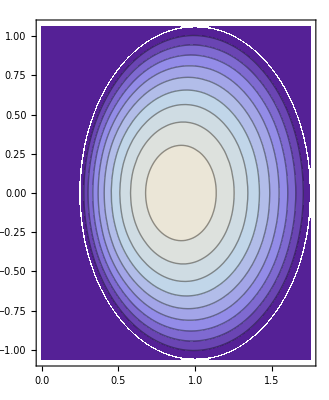

```mathematica
ContourPlot[ ϕ[r,z]Boole[Z[r,z]≤ 0],{r,0,R+a},{z,-Sqrt[2]a,Sqrt[2]a},AspectRatio->Automatic,PlotRange->All]
```

6.1.6

(6)  Solve the time-dependent (dimensionless) Schrödinger equation for the wave function ψ(x,t) of a particle in a potential V(x), subject to boundary conditions ψ(±a,t)=0 and initial condition  ψ(x,0)=ψ_o(x):

ⅈ (∂ψ(x,t))/(∂t)=V(x) ψ(x,t)-1/2(∂^2 ψ(x,t))/(∂x^2).

Take V(x)=x^4/4, use trigonometric functions for the modes in the Galerkin method, and work out the matrix elements of V(x), V_(n m), analytically for general n and m.  (Note: Check to make sure the integrals for V_(n n) are evaluated properly.) Take ψ_o(x) = exp[-2(x-1)^2], and a = 4. Keep as many basis functions as necessary to obtain a converged answer. Plot the solution in time increments of 0.1 for 0 <t<4.

### Solution

```mathematica
Clear["Global`*"]
```

initial condition:

```mathematica
ϕ0[x_] =  Exp[-2(x-1)^2 ]
```

ⅇ^(-2 (-1+x)^2)

potential:

```mathematica
v[x_] = x^4/4
```

x^4/4

basis functions:

```mathematica
ψ[n_,x_] = Sin[Pi n(x+4)/8];
```

```mathematica
Integrate[ψ[n,x] ψ[m,x] v[x] ,{x,-4,4}]2/8
```

1/π^5 64 ((8 π (-24+m^2 π^2-2 m n π^2+n^2 π^2))/(m-n)^4-(8 π (-24+m^2 π^2+2 m n π^2+n^2 π^2))/(m+n)^4+1/(m-n)^5(8 (m-n) π (-24+m^2 π^2-2 m n π^2+n^2 π^2) Cos[(m-n) π]+(384-48 n^2 π^2+m^4 π^4-4 m^3 n π^4+n^4 π^4+6 m^2 π^2 (-8+n^2 π^2)+m (96 n π^2-4 n^3 π^4)) Sin[(m-n) π])-1/(m+n)^5(8 (m+n) π (-24+m^2 π^2+2 m n π^2+n^2 π^2) Cos[(m+n) π]+(384-48 n^2 π^2+m^4 π^4+4 m^3 n π^4+n^4 π^4+4 m n π^2 (-24+n^2 π^2)+6 m^2 π^2 (-8+n^2 π^2)) Sin[(m+n) π]))

```mathematica
vmat[m_,n_] =%;
```

```mathematica
vmat[m_,m_]=Limit[vmat[m,n],n->m]
```

(32 (2 m π (60-10 m^2 π^2+m^4 π^4)-20 m π (-6+m^2 π^2) Cos[2 m π]-5 (24-12 m^2 π^2+m^4 π^4) Sin[2 m π]))/(5 m^5 π^5)

```mathematica
solution := ((* DEFINE THE NORM *)
normn[f_,g_] := NIntegrate[f  g,{x,-4,4},MaxRecursion->12](2/8);(* DEFINE LIST OF UNKNOWNS *)
coeff = Table[a[n][t],{n,1,nn}];
(* DEFINE INITIAL CONDITIONS *)
Do[f[m] = normn[ψ[m,x],ϕ0[x]];Print["f",m,f[m]],{m,1,nn}];initcond = Table[a[m][0]==f[m],{m,1,nn}];
Print["done initial conditions"];
(* DEFINE ODES SATISFIED BY UNKNOWNS *)ODEs = Table[I  D[a[m][t],t] == ( m Pi/8)^2  a[m][t]+ Sum[(vmat[m,n]) a[n][t],{n,1,nn}],{m,1,nn}] ;
Print["done ODES"];
(* SOLVE THE ODES *)sol = NDSolve[Join[ODEs,initcond],coeff,{t,0,4}];
(* THE SOLUTION IN TERMS OF 'EIGENFUNCTION' EXPANSION *)u[x_,t_] = Sum[a[n][t] ψ[n,x],{n,1,nn}] /.sol[[1]];)
```

```mathematica
nn=20;
```

```mathematica
solution
```

f10.283951

f2-0.205115

f3-0.100808

f40.230172

f5-0.0740537

f6-0.110689

f70.112565

f8-7.27214×10^-11

f9-0.0607445

f100.032234

f110.0116376

f12-0.0195197

f130.0046134

f140.00506559

f15-0.00378426

f16-1.24578×10^-10

f170.00110203

f18-0.000429587

f19-0.000113934

f200.000140384

done initial conditions

done ODES

```mathematica
Table[Plot[Abs[u[x,t]],{x,-4,4},PlotRange->{0,1.5}],{t,0,4,.1}];
```

```mathematica
ListAnimate[%]
```

6.2.5

(5)(a) Use the CTCS method to finite-difference the wave equation in D dimensions (on a uniform Cartesian grid with the same stepsize Δx in each dimension). Perform a von Neumann  stability analysis to show that this method is stable provided that c Δt/Δx ≤  1/√D.

(b) For the 1-D wave equation,  (∂^2 y)/(∂t^2)=c^2 (x)(∂^2 y(x,t))/(∂x^2)on -4<x<4,  where c(x) = 1 for x<0 and c(x) =1/2  for x≥ 0, use the CTCS method to solve the following problem for 0<t<20. Take Δx = 0.25,  Δt=0.2:

y(x,0)=ⅇ^(-2(x-2)^2), (∂y(x,t))/(∂t)|_(t=0)=-4(x-2) ⅇ^(-2(x-2)^2), y(-4,t) =y(4,t) = 0.

Make an animation of the result showing every second time step. Note: The CTCS scheme will require you to specify  y_k^1 directly from the two initial conditions. To determine y_k^1use the equation for uniform acceleration,

y_k^1=y_k^0+v_(0 k)Δt  + a_k Δt^2/2,

where v_(o k) is the initial velocity of the kth point and a_k is the initial acceleration, determined by

a_k= c^2 (∂^2 y(x,0))/(∂x^2)|_(x=x_k) .

### Solution

#### part (a)

The wave equation becomes

y_(j k l ...)^(n+1)=2 y_(j k l ...)^n-y_(j k l ...)^(n-1)+(c^2 Δt^2)/Δx^2(y_(j+1 k l ...)^n-2 y_(j k l ...)^n+y_(j-1 k l ...)^n)+(c^2 Δt^2)/Δy^2(y_(j k+1 l ...)^n-2 y_(j k l ...)^n+y_(j k-1 l ...)^n )+....
Write solution as y_(j k l ...)^n = ζ^n ⅇ^(ⅈ k·r). Then this equation becomes
ζ = 2 - 1/ζ+(c^2 Δt^2)/Δx^2(ⅇ^(ⅈ k_x Δx)-2 + ⅇ^(-ⅈ k_x Δx)) + (c^2 Δt^2)/Δy^2(ⅇ^(ⅈ k_y Δy)-2 + ⅇ^(-ⅈ k_y Δy))+...
   = 2 -  1/ζ-c^2 Δt^2∑_(n=1)^D 4/Δr_n^2 sin^2 k_n Δr_n/2

where Δr_nis the nth component of Δr= (Δx,Δy,...). Now define α =c^2 Δt^2∑_(n=1)^D 4/Δr_n^2 sin^2 k_n Δr_n/2 . Then this equation is the same as for the 1D case:
ζ = 2 - 1/ζ - α, which implies that ζ  is

```mathematica
ζ/.Solve[ζ^2 ==(2- α)ζ -1,ζ]
```

{1/2 (2-√(-4+α) √α-α),1/2 (2+√(-4+α) √α-α)}

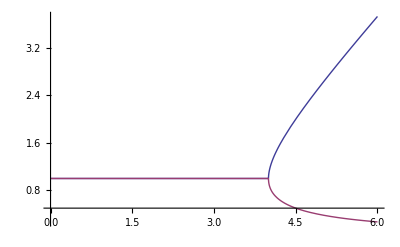

```mathematica
Plot[Evaluate[Abs[%]],{α,0,6},PlotRange->All]
```

Maxmimum value of α for stability is α = 4. So c^2 Δt^2∑_(n=1)^D 4/Δr_n^2 sin^2 k_n Δr_n/2≤ 4 for stability. The largest value the sum can be is if k_n Δr_n=π for every n so that c^2 Δt^2∑_(n=1)^D 4/Δr_n^2≤ 4, or 
	
					c Δt ≤ 1/(√(∑_(n=1)^D Δr_n^-2))

For the case where Δr_n=Δx for all directions, this becomes c Δt ≤ Δx/√D.

#### part (b)

```mathematica
Clear["Global`*"];
```

```mathematica
(* define the grid *)
M=32; 
L=8.;
Δx = L/M; 
Δt = 0.2;
x[j_] := j Δx - L/2;
```

```mathematica
c[x_] = 1 - 1/2 UnitStep[x];
```

```mathematica
(* initial conditions *)
y0[j_] := Exp[-2(x[j]-2)^2];
v0[j_] := -2(x[j]-2)Exp[-2(x[j]-2)^2];
```

```mathematica
(* zeroth step: *)
y[j_,0] := y0[j];
```

```mathematica
(* boundary conditions *)
y[0,n_] := 0;
y[M,n_] := 0;
```

We construct the recursion relation for this method below:

```mathematica
y[j_,n_] := (y[j,n] = 2 y[j,n-1] -y[j,n-2] +  (Δt^2 c[x[j]]^2)/Δx^2(y[j+1,n-1] - 2 y[j,n-1] + y[j-1,n-1])) /; n≥ 2
```

The method can only be used for n≥ 2 because evaluation of the nth time step  refers back to the n-2nd step. Therefore, for the first step, we use the trick employed in Chapter 1 for second-order ODEs [see Eq. (1.4.28) and the surrounding discussion]:

y_j^1=y_j^0+v_o_j Δt+Δt^2/2 a_j,
where v_o_(j k) is the initial velocity (equal to zero for our choice of initial conditions), and a_(j k) is the initial acceleration, given by

a_j=c_j^2/Δx^2(y_(j+1)^0-2 y_j^0+y_(j-1)^0).

```mathematica
y[j_,1] := (y[j,1]=y[j,0]+ v0[j] Δt + Δt^2 c[x[j]]^2 (y[j+1,0]-2y[j,0]+y[j-1,0])/(2 Δx^2) )/; 1≤ j≤ M
```

(Of course, this cell must be modified if other initial conditions are used.) At each time step, we construct an interpolation function of the solution in x and y:

```mathematica
Clear[ysol]
```

```mathematica
ysol[n_] := ysol[n] = Interpolation[Table[{x[j],y[j,n]},{j,0,M}]]
```

In Cell 6.77 we plot the solution.

```mathematica
ysol[1]
```

InterpolatingFunction[{{-4., 4.}}, <>]

```mathematica
Table[Plot[Evaluate[ysol[n][x]],{x,-4,4},PlotRange->{-2,2}],{n,0,10/0.2,5}];
```

```mathematica
ListAnimate[%]
```

6.2.8

(8)(a) For the 1-D Schrödinger equation and for a particle of mass m in a uniform potential V(x)=V_o, show that the Crank-Nicolson method is stable for any time step size.

(b) Use the Crank-Nicolson method to solve the Schrödinger equation for a particle of mass m, described by a wave function ψ(x,t), moving in a potential V(x) = 8 x on -4<x<4, over the time range 0<t<3. Animate (|ψ|)^2 over this time interval. Take ψ=0 on the boundaries, and assume an initial condition ψ(x,0)=ⅇ^(5 ⅈ x -2 (x+2)^2). Also, take m=ℏ=1.

### Solution

#### part a

The 1D Shrodinger equation is

ⅈ ℏ∂/(∂t)ψ(x,t)=-ℏ^2/(2 m)∂^2/(∂x^2)ψ(x,t) + V_o ψ(x,t). Crank-Nicolson on this equation yields
		ⅈ ℏ (ψ_j^n-ψ_j^(n-1))/Δt=-ℏ^2/(4 m)((ψ_(j+1)^n-2 ψ_j^n+ψ_(j-1)^n)/Δx^2+(ψ_(j+1)^(n-1)-2 ψ_j^(n-1)+ψ_(j-1)^(n-1))/Δx^2)+V_o(ψ_j^n+ψ_j^(n-1))/2.

Now assume that ψ_j^n=ζ^n ⅇ^(ⅈ k x_j) and we obtain the following equation for ζ:
ⅈ ℏ(ζ-1)/Δt=ℏ^2/(m Δx^2)(ζ+1) sin^2(k Δx/2)+V_o(ζ+1)/2. So ζ - 1 = -ⅈ Δt/ℏ(ζ+1) (ℏ^2/(m Δx^2) sin^2(k Δx/2)+V_o/2). This implies that
ζ = (1-ⅈ Δt/ℏ ζ (ℏ^2/(m Δx^2) sin^2(k Δx/2)+V_o/2))/(1+ⅈ Δt/ℏ ζ (ℏ^2/(m Δx^2) sin^2(k Δx/2)+V_o/2)). The magnitude of this complex number is always equal to one, so the method is stable.

#### part b

```mathematica
Clear["Global`*"]
```

By repeating the simulation at ever-decreasing timestep and comparing results to observe the convergence, I have determined  that the required time stepsize is quite small for reasonable accuracy over the length of the simulation, if I take 120 grid points in x.

```mathematica
V[x_] = 8 x;
M=120;
L=8.;
Δx = L/M;
Δt = 0.0125/2;
x[j_] = j Δx - L/2;
```

```mathematica
ψ0[j_] = Exp[5 I x[j]-2(x[j]+2)^2];
```

```mathematica
ψ[0,n_] = ψ[M,n_] = 0;
```

```mathematica
sol[0] = Table[ψ[j,0]-> ψ0[j ],{j,1,M-1}]
```

{ψ[1,0]→0.000387859-0.000413273 ⅈ,ψ[2,0]→0.000832747-0.000437543 ⅈ,ψ[3,0]→0.00151649-0.000229883 ⅈ,ψ[4,0]→0.00241584+0.000446825 ⅈ,ψ[5,0]→0.00336215+0.00190821 ⅈ,ψ[6,0]→0.00394607+0.00448792 ⅈ,ψ[7,0]→0.00343267+0.00840083 ⅈ,ψ[8,0]→0.000738477+0.0135183 ⅈ,ψ[9,0]→-0.00545954+0.0190752 ⅈ,ψ[10,0]→-0.0164132+0.0233794 ⅈ,ψ[11,0]→-0.0327554+0.0236509 ⅈ,ψ[12,0]→-0.053758+0.0161614 ⅈ,ψ[13,0]→-0.0765553-0.00316327 ⅈ,ψ[14,0]→-0.0956141-0.0375954 ⅈ,ψ[15,0]→-0.102813-0.0880069 ⅈ,ψ[16,0]→-0.0884588-0.151148 ⅈ,ψ[17,0]→-0.0433939-0.218365 ⅈ,ψ[18,0]→0.038018-0.275426 ⅈ,ψ[19,0]→0.154635-0.304044 ⅈ,ψ[20,0]→0.29601-0.285292 ⅈ,ψ[21,0]→0.441702-0.204517 ⅈ,ψ[22,0]→0.563309-0.0566879 ⅈ,ψ[23,0]→0.629419+0.149392 ⅈ,ψ[24,0]→0.612764+0.389632 ⅈ,ψ[25,0]→0.497932+0.627092 ⅈ,ψ[26,0]→0.287443+0.818418 ⅈ,ψ[27,0]→0.00408543+0.923107 ⅈ,ψ[28,0]→-0.311726+0.913337 ⅈ,ψ[29,0]→-0.609444+0.781637 ⅈ,ψ[30,0]→-0.839072+0.544021 ⅈ,ψ[31,0]→-0.962295+0.237417 ⅈ,ψ[32,0]→-0.961037-0.0881274 ⅈ,ψ[33,0]→-0.841079-0.380433 ⅈ,ψ[34,0]→-0.629871-0.596402 ⅈ,ψ[35,0]→-0.369303-0.71049 ⅈ,ψ[36,0]→-0.105655-0.718422 ⅈ,ψ[37,0]→0.120468-0.635589 ⅈ,ψ[38,0]→0.281629-0.491137 ⅈ,ψ[39,0]→0.366964-0.31979 ⅈ,ψ[40,0]→0.381252-0.153818 ⅈ,ψ[41,0]→0.340679-0.0170987 ⅈ,ψ[42,0]→0.266963+0.0776879 ⅈ,ψ[43,0]→0.181647+0.128727 ⅈ,ψ[44,0]→0.101892+0.142439 ⅈ,ψ[45,0]→0.0383895+0.129776 ⅈ,ψ[46,0]→-0.00469587+0.102632 ⅈ,ψ[47,0]→-0.028353+0.0711817 ⅈ,ψ[48,0]→-0.0366921+0.0424829 ⅈ,ψ[49,0]→-0.0349589+0.0202523 ⅈ,ψ[50,0]→-0.028042+0.00544367 ⅈ,ψ[51,0]→-0.0196425-0.00279998 ⅈ,ψ[52,0]→-0.0120401-0.00619076 ⅈ,ψ[53,0]→-0.00626869-0.00656207 ⅈ,ψ[54,0]→-0.0024869-0.00543398 ⅈ,ψ[55,0]→-0.00037006-0.00384817 ⅈ,ψ[56,0]→0.000577936-0.00238787 ⅈ,ψ[57,0]→0.000828721-0.00129066 ⅈ,ψ[58,0]→0.000739282-0.000581699 ⅈ,ψ[59,0]→0.000535574-0.000185444 ⅈ,ψ[60,0]→0.000335463+0. ⅈ,ψ[61,0]→0.00018432+0.0000638214 ⅈ,ψ[62,0]→0.0000875619+0.0000688975 ⅈ,ψ[63,0]→0.0000337805+0.00005261 ⅈ,ψ[64,0]→8.10755×10^-6+0.0000334982 ⅈ,ψ[65,0]→-1.78663×10^-6+0.0000185788 ⅈ,ψ[66,0]→-4.13213×10^-6+9.02887×10^-6 ⅈ,ψ[67,0]→-3.58463×10^-6+3.7524×10^-6 ⅈ,ψ[68,0]→-2.36947×10^-6+1.21833×10^-6 ⅈ,ψ[69,0]→-1.33036×10^-6+1.89639×10^-7 ⅈ,ψ[70,0]→-6.53634×10^-7-1.26887×10^-7 ⅈ,ψ[71,0]→-2.80437×10^-7-1.62463×10^-7 ⅈ,ψ[72,0]→-1.01299×10^-7-1.17286×10^-7 ⅈ,ψ[73,0]→-2.6939×10^-8-6.76319×10^-8 ⅈ,ψ[74,0]→-1.53551×10^-9-3.35599×10^-8 ⅈ,ψ[75,0]→4.32017×10^-9-1.46044×10^-8 ⅈ,ψ[76,0]→3.94621×10^-9-5.51658×10^-9 ⅈ,ψ[77,0]→2.42115×10^-9-1.71579×10^-9 ⅈ,ψ[78,0]→1.22461×10^-9-3.56369×10^-10 ⅈ,ψ[79,0]→5.37829×10^-10+2.69937×10^-11 ⅈ,ψ[80,0]→2.0714×10^-10+8.35716×10^-11 ⅈ,ψ[81,0]→6.86162×10^-11+5.97954×10^-11 ⅈ,ψ[82,0]→1.81232×10^-11+3.16052×10^-11 ⅈ,ψ[83,0]→2.66796×10^-12+1.40762×10^-11 ⅈ,ψ[84,0]→-8.05286×10^-13+5.47571×10^-12 ⅈ,ψ[85,0]→-9.68717×10^-13+1.86368×10^-12 ⅈ,ψ[86,0]→-5.68615×10^-13+5.384×10^-13 ⅈ,ψ[87,0]→-2.6131×10^-13+1.18195×10^-13 ⅈ,ψ[88,0]→-1.02757×10^-13+9.42286×10^-15 ⅈ,ψ[89,0]→-3.54105×10^-14-8.73647×10^-15 ⅈ,ψ[90,0]→-1.06261×10^-14-6.88957×10^-15 ⅈ,ψ[91,0]→-2.65621×10^-15-3.4067×10^-15 ⅈ,ψ[92,0]→-4.67579×10^-16-1.36998×10^-15 ⅈ,ψ[93,0]→2.10898×10^-18-4.76526×10^-16 ⅈ,ψ[94,0]→5.10668×10^-17-1.45399×10^-16 ⅈ,ψ[95,0]→3.04445×10^-17-3.83416×10^-17 ⅈ,ψ[96,0]→1.28939×10^-17-8.19873×10^-18 ⅈ,ψ[97,0]→4.5581×10^-18-1.08186×10^-18 ⅈ,ψ[98,0]→1.40392×10^-18+1.41282×10^-19 ⅈ,ψ[99,0]→3.7886×10^-19+1.7542×10^-19 ⅈ,ψ[100,0]→8.73792×10^-20+8.42154×10^-20 ⅈ,ψ[101,0]→1.57095×10^-20+3.08881×10^-20 ⅈ,ψ[102,0]→1.32922×10^-21+9.62968×10^-21 ⅈ,ψ[103,0]→-5.22142×10^-22+2.6275×10^-21 ⅈ,ψ[104,0]→-3.66314×10^-22+6.25916×10^-22 ⅈ,ψ[105,0]→-1.46525×10^-22+1.25424×10^-22 ⅈ,ψ[106,0]→-4.68964×10^-23+1.84396×10^-23 ⅈ,ψ[107,0]→-1.29225×10^-23+5.33957×10^-25 ⅈ,ψ[108,0]→-3.12295×10^-24-9.38861×10^-25 ⅈ,ψ[109,0]→-6.54874×10^-25-4.7285×10^-25 ⅈ,ψ[110,0]→-1.12933×10^-25-1.60864×10^-25 ⅈ,ψ[111,0]→-1.29282×10^-26-4.51699×10^-26 ⅈ,ψ[112,0]→6.01824×10^-28-1.10168×10^-26 ⅈ,ψ[113,0]→9.62758×10^-28-2.35618×10^-27 ⅈ,ψ[114,0]→3.80892×10^-28-4.33194×10^-28 ⅈ,ψ[115,0]→1.11688×10^-28-6.33895×10^-29 ⅈ,ψ[116,0]→2.76192×10^-29-5.10834×10^-30 ⅈ,ψ[117,0]→5.96669×10^-30+9.04488×10^-31 ⅈ,ψ[118,0]→1.12762×10^-30+5.92474×10^-31 ⅈ,ψ[119,0]→1.80748×10^-31+1.92592×10^-31 ⅈ}

Note that we need not add the end points to the list, since they are already determined by the boundary conditions. We can then write the Crank-Nicolson method as the following recursion relation on sol[n]:

```mathematica
sol[n_] := sol[n] = 
Module[{vars,eqns},
(*define the variables*)
 vars= Table[ψ[j,n],{j,1,M-1}]; 
(*define the equations (Eqs. 6.2.16),substituting for the values of T determined at the last time step  *)
eqns= Table[I (ψ[j,n]-ψ[j,n-1]) ==Δt/2( V[x[j]](ψ[j,n]+ψ[j,n-1])+-1/(2 Δx^2)(ψ[j+1,n]-2ψ[j,n]+ψ[j-1,n]+ψ[j+1,n-1]-2ψ[j,n-1]+ψ[j-1,n-1])),{j,1,M-1}]/.sol[n-1];
(*solve the equations *)
Solve[eqns,vars][[1]]]
```

```mathematica
Table[ListPlot[Table[{x[j],Abs[ψ[j,n]]^2},{j,0,M}]/.sol[n],Joined->True,PlotRange->{{-4,4},{-1,1}},AxesLabel->{"x",""},PlotLabel->"|ψ[x,t]|^2,t="<>ToString[Δt n]],{n,0,3/Δt,16}];
```

```mathematica
ListAnimate[%]
```